```mathematica
(*CloseKernels[];LaunchKernels[];*)
SetDirectory[NotebookDirectory[]];
ClearAll[Evaluate[Context[]<>"*"]];

<<FirstIteration.m
<<Test.m
<<Spektr.m

(*
test1 = Function[{kp,op}, Block[{alpha, al1,  al2,al3,al4,al5, al6,al7,al8, coeffs},
alpha = findAlpha[kp,op];
coeffs = findCoeffsAndDet[{al1, al2,al3,al4,al5, al6,al7,al8},kp,op];
{al1, al2,al3,al4,al5, al6,al7,al8} = alpha;
coeffs
]];

test2 = Function[{kp1,op1}, Block[{kp, op,alpha, al1,  al2,al3,al4,al5, al6,al7,al8, coeffs},
alpha = findAlpha[kp,op];
coeffs = findCoeffsAndDet[{al1, al2,al3,al4,al5, al6,al7,al8},kp,op];
{al1, al2,al3,al4,al5, al6,al7,al8} = alpha;
kp = kp1;
op=op1;
coeffs
]];

test3 = Function[{kp, op}, Block[{alpha, al1,  al2,al3,al4,al5, al6,al7,al8, coeffs},
alpha = findAlpha[kp,op];
coeffs = findCoeffsAndDet[alpha,kp,op];
{al1, al2,al3,al4,al5, al6,al7,al8} = alpha;
coeffs
]];
*)

Coeffs = findCoeffsAndDet[{al1, al2,al3,al4,al5, al6,al7,al8},kp,op];
{al1, al2,al3,al4,al5, al6,al7,al8} = findAlpha[kp,op];


dis = Function[{k, o},Block[{kp,op},
kp = k;op =o;

Check[Det[ Coeffs],Infinity]
]];

fx[k1_?NumberQ,o1_?NumberQ] :=dis[k1, o1];

(*fx[kp_?NumberQ,ops_?NumberQ, opf_] :=Join[Map[(dis[kp, #])&,Range[ops,opf,0.1]]];
*)
PrintTemporary["Working ...."];

DistributeDefinitions[fx,dis,Coeffs,al1, al2,al3,al4,al5, al6,al7,al8];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Map[(fx[#,1,5])&,Range[1,2,0.1]]//AbsoluteTiming
*)
dispersionPoints = Parallelize[
Map[
Function[{x},
Map[
{x,#,(Abs[fx[x, #]] < 0.001)}&,Range[0,10,0.001]
]
], Range[0,10,0.001]

],
Method->"FinestGrained"
]
Flatten[dispersionPoints,1];


(*dispersionPoints[[2]] >> "dispertionPoints.m"*)


(*Plot3D[fx[kp,op],{kp,1,20},{op,1,20},PlotRange->0, Filling->0, FillingStyle->{Red,Blue}]
*)


(*ParallelMap[(Print[$KernelID];fx[3,#])&,{2,3,4,5,6,7,8,9}] // AbsoluteTiming
*)





(*CloseKernels[];LaunchKernels[];

fx[kp_?NumberQ,op_?NumberQ] :=dispersion[kp, op];*)
```

Parallelize::nopar1: Flatten[Function[{x}, ({x, #1, Abs[« 1 »] < 0.001} &)/@Range[0, 10, 0.001]]/@Range[0, 10, 0.001], 1] cannot be parallelized; proceeding with sequential evaluation.

Power::infy: Infinite expression 1/0.^1/3 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^1/3 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^1/3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

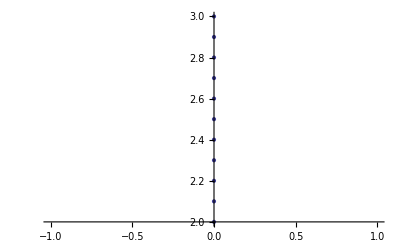

```mathematica
ListPlot[Map[Most@#&,Select[dispersionPoints,#[[3]]&]]]
```

```mathematica
ListPlot[{dis[0,2]}]
```

Power::infy: Infinite expression 1/0. + 0.\ ⅈ encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. + 0.\ ⅈ encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. + 0.\ ⅈ encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0. + 0.\ ⅈ)\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Det::mindet: Input matrix contains an indeterminate entry.

-Graphics-

```mathematica
ListContourPlot[dispersionPoints,PlotLegends->Automatic,DataRange->{{2,3},{0,1}}]
```

-Graphics-

```mathematica
(*
CloseKernels[];LaunchKernels[];
ParallelDo[dispersion[x, y],{x,1.7975,20, 0.01},{y,2.263,2.270, 0.01}] // AbsoluteTiming;
dispersion[1.7975, 2.263];
*)
```

```mathematica
roots = Map[Map[(Abs[#]<100)&,#]&, dispersionPoints];
ListContourPlot[roots,PlotLegends->Automatic,DataRange->{{2,3},{0,1}}]
```

ListContourPlot::arrayerr: dispersionPoints must be a valid array.

ListContourPlot[dispersionPoints,PlotLegends→Automatic,DataRange→{{2,3},{0,1}}]

{{Abs[Det[SparseArray[<64>,{8,8}]]]<100,True,True,True,True,Abs[Det[SparseArray[<64>,{8,8}]]]<100,True,True,True,True,True},{False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False,False}}